# Big Data Analytics Class Assignment - Week 9

## by: Dhewa Radya | 6701011256

## Task 1. Make an Classification ML Model on Titanic Dataset

#### Import the dataset

```mathematica
ExampleData[{"MachineLearning","Titanic"},"Properties"]
```

{Data,Description,Data,Dimensions,LearningTask,LongDescription,MissingData,Name,Source,TestData,TrainingData,VariableDescriptions,VariableTypes}

```mathematica
df = ExampleData[{"MachineLearning","Titanic"},"Data"];
dftrain = ExampleData[{"MachineLearning","Titanic"},"TrainingData"];
dftest = ExampleData[{"MachineLearning","Titanic"},"TestData"];
```

```mathematica
Take[df, 5]
```

{{1st,29.,female}→survived,{1st,0.9167,male}→survived,{1st,2.,female}→died,{1st,30.,male}→died,{1st,25.,female}→died}

```mathematica
ExampleData[{"MachineLearning","Titanic"},"LongDescription"]
```

This data set contains the survival status of 1309 passengers aboard the maiden voyage of the RMS Titanic in 1912 
	(the ships crew are not included), along with the passengers age, sex and class (which serves as a proxy for economic status). 

	70% of the data was selected (using stratified sampling) for the training set.

#### Exploratory Data Analysis

```mathematica
ExampleData[{"MachineLearning","Titanic"},"MissingData"]
```

True

```mathematica
ExampleData[{"MachineLearning","Titanic"},"VariableDescriptions"]
```

{passenger class,passenger age,passenger sex}→passenger survival

```mathematica
ExampleData[{"MachineLearning","Titanic"},"VariableTypes"]
```

{Nominal,Numerical,Nominal}→Nominal

```mathematica
Count[Flatten[df], _Missing]
```

0

### Machine Learning Model

```mathematica
dt = Classify[dftrain, Method->"DecisionTree"]
lr = Classify[dftrain, Method->"LogisticRegression"]
rf = Classify[dftrain, Method->"RandomForest"]
gb = Classify[dftrain, Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierFunction[…]

«1 more identical outputs»

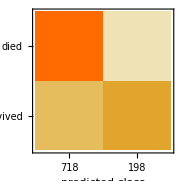
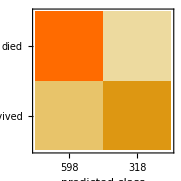
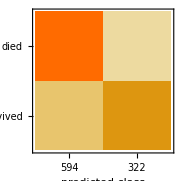
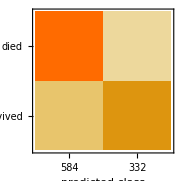
Decision Tree | Logistic Regression | Random Forest | Gradient Boosting
Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 916
Accuracy | (79.31.3) %
Accuracy baseline | (61.81.6) %
Geometric mean of probabilities | 0.617 ± 0.0098
Mean cross entropy | 0.483 ± 0.016
Single evaluation time | 6.08 ms/example
Batch evaluation speed | 8.13 examples/ms
-Graphics- |  | Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 916
Accuracy | (78.81.4) %
Accuracy baseline | (61.81.6) %
Geometric mean of probabilities | 0.625 ± 0.011
Mean cross entropy | 0.47 ± 0.017
Single evaluation time | 5.6 ms/example
Batch evaluation speed | 10. examples/ms
-Graphics- |  | Classifier Measurements
Classifier method | RandomForest
Number of test examples | 916
Accuracy | (79.71.3) %
Accuracy baseline | (61.81.6) %
Geometric mean of probabilities | 0.633 ± 0.009
Mean cross entropy | 0.457 ± 0.014
Single evaluation time | 6.21 ms/example
Batch evaluation speed | 6.71 examples/ms
-Graphics- |  | Classifier Measurements
Classifier method | GradientBoostedTrees
Number of test examples | 916
Accuracy | (78.61.4) %
Accuracy baseline | (61.81.6) %
Geometric mean of probabilities | 0.641 ± 0.011
Mean cross entropy | 0.445 ± 0.017
Single evaluation time | 9.74 ms/example
Batch evaluation speed | 8.69 examples/ms
-Graphics- |

```mathematica
classifierDT = ClassifierMeasurements[dt, dftrain];
classifierLR = ClassifierMeasurements[lr, dftrain];
classifierRF = ClassifierMeasurements[rf, dftrain];
classifierGB = ClassifierMeasurements[gb, dftrain];

TableForm[{
  {"Decision Tree", "Logistic Regression", "Random Forest", "Gradient Boosting"},
  {classifierDT, classifierLR, classifierRF, classifierGB}
}]
```

```mathematica
classifierDT = ClassifierMeasurements[dt, dftrain];
classifierLR = ClassifierMeasurements[lr, dftrain];
classifierRF = ClassifierMeasurements[rf, dftrain];
classifierGB = ClassifierMeasurements[gb, dftrain];


metricsList = {
   {"Classifier", "Accuracy", "Precision", "Recall", "F1 Score"},
   {
     "Decision Tree", 
     classifierDT["Accuracy"], 
     classifierDT["Precision"], 
     classifierDT["Recall"], 
     classifierDT["F1Score"]
   },
   {
     "Logistic Regression", 
     classifierLR["Accuracy"], 
     classifierLR["Precision"], 
     classifierLR["Recall"], 
     classifierLR["F1Score"]
   },
   {
     "Random Forest", 
     classifierRF["Accuracy"], 
     classifierRF["Precision"], 
     classifierRF["Recall"], 
     classifierRF["F1Score"]
   },
   {
     "Gradient Boosting", 
     classifierGB["Accuracy"], 
     classifierGB["Precision"], 
     classifierGB["Recall"], 
     classifierGB["F1Score"]
   }
};


TableForm[metricsList, TableHeadings -> {None, {"Metric", "Value"}}]
```

Metric | Value |  |  | 
Classifier | Accuracy | Precision | Recall | F1 Score
Decision Tree | 0.792576 | <|died→0.761838,survived→0.90404|> | <|died→0.966431,survived→0.511429|> | <|died→0.852025,survived→0.653285|>
Logistic Regression | 0.78821 | <|died→0.811037,survived→0.745283|> | <|died→0.85689,survived→0.677143|> | <|died→0.833333,survived→0.709581|>
Random Forest | 0.796943 | <|died→0.819865,survived→0.754658|> | <|died→0.860424,survived→0.694286|> | <|died→0.839655,survived→0.723214|>
Gradient Boosting | 0.786026 | <|died→0.816781,survived→0.731928|> | <|died→0.842756,survived→0.694286|> | <|died→0.829565,survived→0.71261|>

we see that the Random Forest has the best performance among the others.

### Fit to Data Test

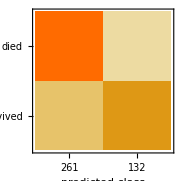
Random Forest on Test Dataset
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 393
Accuracy | (79.12.1) %
Accuracy baseline | (61.82.5) %
Geometric mean of probabilities | 0.619 ± 0.015
Mean cross entropy | 0.48 ± 0.023
Single evaluation time | 14.6 ms/example
Batch evaluation speed | 4.04 examples/ms
-Graphics- |

```mathematica
testRF = ClassifierMeasurements[rf, dftest];

TableForm[{
  {"Random Forest on Test Dataset"},
  {testRF}
}]
```

We can see that the train and test dataset have the similar level of accuracy, so can refers that it is not overfitting / underfitting

## Task 2. What is Gini Impurity

Gini impurity is a measure used in decision trees to evaluate the quality of a split. It quantifies how often a randomly chosen element from the set would be incorrectly labeled if it was randomly labeled according to the distribution of labels in the subset.

### Definition

Gini impurity measures the likelihood of misclassified a randomly chosen element from a dataset. It ranges from 0 to 0.5 for binary classification, where:

0 indicates perfect purity (all elements belong to a single class).

0.5 indicates maximum impurity (elements are evenly distributed across classes).

### Formula

Gini = 1 - ∑_(i=1)^c (P_i)^2

### Usage

In constructing decision trees, Gini impurity is used to select the best feature to split the data. The feature that results in the lowest Gini impurity after the split is preferred.

When building a decision tree, the goal is to create branches that lead to pure leaf nodes (nodes where all samples belong to a single class). By measuring the Gini impurity, we can assess how well a particular feature divides the dataset. Features that yield lower Gini impurity values after splitting indicate better separation between classes, guiding the tree-building process.

Overall, Gini impurity is a crucial concept in machine learning, particularly in classification tasks, providing a straightforward way to evaluate the effectiveness of different features in decision tree algorithms.